# LabQuest2

#### code

```mathematica
base="http://140.177.208.85";
start:=URLExecute[base<>"/control/start"];
stop:=URLExecute[base<>"/control/stop"];
status:=Import[base<>"/status","RawJSON"];
columns[c_String]:=Import[base<>"/columns/"<>c,"RawJSON"];
process[values_,label1_,label2_]:=Transpose[{values[label1],values[label2]}];
```

```mathematica
LabQuest2[]:=Module[{cols,sets,set,names,units,values,data},
start;
Pause[3];
cols=status["columns"];
sets=GroupBy[Map[#["setID"]&,cols],Identity,Keys];
set=First[sets];
names=Map[#["name"]&,cols];
units=Map[#["units"]&,cols];
values=Association@Map[names[#]->columns[#]["values"]&,set];
data=Map[process[values,"Time",#]&,{"X Acceleration","Y Acceleration","Z Acceleration"}];
Print@ListLinePlot[data,Frame->True,Filling->Axis];
]
```

```mathematica
Button["Run Experiment",LabQuest2[]]
```

Run Experiment

-Graphics-

```mathematica
LabQuest2[]:=Module[{cols,sets,set,names,units,values,data},
start;
Pause[3];
cols=status["columns"];
sets=GroupBy[Map[#["setID"]&,cols],Identity,Keys];
set=First[sets];
names=Map[#["name"]&,cols];
units=Map[#["units"]&,cols];
values=Association@Map[names[#]->columns[#]["values"]&,set];
data=Map[process[values,"Time",#]&,{"Illumination"}];
Print@ListLinePlot[data,Frame->True,Filling->Axis];
]
```

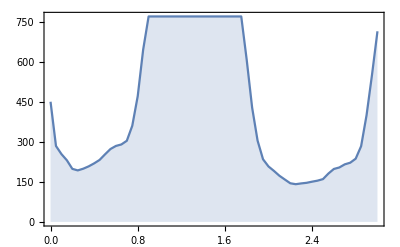

```mathematica
LabQuest2[]
```

```mathematica
status
```

<|sessionID→4t1505835405ut907185u0p8898r2126859589k3199177628,sessionDesc→,columnListTimeStamp→1505835629,viewListTimeStamp→1505835629,requestTimeStamp→1505835629,views→<|176→<|id→176,colID→183,viewType→meter|>,105→<|id→105,baseColID→182,baseMin→0,baseMax→10,leftTraceMin→57,leftTraceMax→65,viewType→graph,title→,connectLines→True,leftTraceColIDs→{183}|>|>,columns→<|182→<|id→182,setID→181,groupID→171,position→0,name→Time,units→s,formatStr→%.2f,liveValue→10.00,liveValueTimeStamp→1505835590,valuesTimeStamp→1505835582,valueCount→67|>,183→<|id→183,setID→181,groupID→174,position→1,name→Illumination,units→lux,formatStr→%.1f,liveValue→61.9,liveValueTimeStamp→1505835589,valuesTimeStamp→1505835582,valueCount→69|>,172→<|id→172,setID→159,groupID→171,position→0,name→Time,units→s,formatStr→%.2f,liveValue→10.00,liveValueTimeStamp→1505835425,valuesTimeStamp→1505835425,valueCount→201|>,175→<|id→175,setID→159,groupID→174,position→1,name→Illumination,units→lux,formatStr→%.1f,liveValue→61.9,liveValueTimeStamp→1505835589,valuesTimeStamp→1505835425,valueCount→201|>|>,sets→<|181→<|name→Run 2,position→1,colIDs→{182,183}|>,159→<|name→Run 1,position→0,colIDs→{172,175}|>|>,collection→<|isCollecting→False,canControl→True|>|>